```mathematica
path="/Users/rumiallbert/Desktop/Wolfram/Project/data/activations/";
```

```mathematica
SetDirectory[path];
```

```mathematica
files=FileNames["*_diff_of_mean_llama3.npy"];
```

```mathematica
pythonSession=StartExternalSession["Python"]
```

ExternalSessionObject[…]

```mathematica
ExternalEvaluate[pythonSession,"
import numpy as np
"]
```

```mathematica
loadFile[filename_]:=ExternalEvaluate[pythonSession,"
data = np.load('"<>path<>filename<>"', allow_pickle=True)
data.tolist()
"]
```

```mathematica
allPersMeanOfDiff=loadFile/@files;
```

```mathematica
personalityNames=StringReplace[StartOfString~~x:Shortest[__]~~"_"~~___~~EndOfString:>x]/@files;
```

```mathematica
Dimensions[allPersMeanOfDiff]
```

{156,31,4096}

```mathematica
(*Association[Thread[personalityNames->allPersMeanOfDiff]]*)
```

```mathematica
(*Transpose[{personalityNames,allPersMeanOfDiff}]*)
```

```mathematica
(*Thread[{personalityNames,allPersMeanOfDiff}]*)
```

```mathematica
Dimensions[allPersMeanOfDiff[[All,18]]]
```

{156,4096}

```mathematica
reducerPCA=DimensionReduction[allPersMeanOfDiff[[All,18]],Method->"PrincipalComponentsAnalysis"]
reducerUMAP=DimensionReduction[allPersMeanOfDiff[[All,18]],Method->"UMAP"]
reducerTSNE=DimensionReduction[allPersMeanOfDiff[[All,18]],Method->"TSNE"]
(*Reduced Dimensions*)
reducedPCA=reducerPCA/@allPersMeanOfDiff[[All,18]];
reducedUMAP=reducerUMAP/@allPersMeanOfDiff[[All,18]];
reducedTSNE=reducerTSNE/@allPersMeanOfDiff[[All,18]];
```

DimensionReducerFunction[…]

DimensionReducerFunction[…]

DimensionReducerFunction[…]

```mathematica
ListPlot[Callout[#1,#2]&@@@Transpose[{reducedPCA,personalityNames}],ImageSize->1000, PlotLegends->personalityNames]
```

-Graphics-

```mathematica
ListPlot[Callout[#1,#2]&@@@Transpose[{reducedUMAP,personalityNames}],ImageSize->1000]
```

-Graphics-

```mathematica
ListPlot[Callout[#1,#2]&@@@Transpose[{reducedTSNE,personalityNames}],ImageSize->1000]
```

-Graphics-

```mathematica
(*Sample 50 personalities*)sampleSize=50;
sampleIndices=RandomSample[Range[Length[personalityNames]],sampleSize];

sampledPersonalityNames=personalityNames[[sampleIndices]];
sampledReducedPCA=reducedPCA[[sampleIndices]];
sampledReducedUMAP=reducedUMAP[[sampleIndices]];
sampledReducedTSNE=reducedTSNE[[sampleIndices]];

(*Define the individual plots with larger ImageSize and no axis tick marks*)
plotPCA=ListPlot[Callout[#1,#2]&@@@Transpose[{sampledReducedPCA,sampledPersonalityNames}],ImageSize->400,PlotLegends->sampledPersonalityNames,PlotLabel->"PCA",Axes->False];

plotUMAP=ListPlot[Callout[#1,#2]&@@@Transpose[{sampledReducedUMAP,sampledPersonalityNames}],ImageSize->500,PlotLabel->"UMAP",Axes->False];

plotTSNE=ListPlot[Callout[#1,#2]&@@@Transpose[{sampledReducedTSNE,sampledPersonalityNames}],ImageSize->500,PlotLabel->"t-SNE",Axes->False];

(*Combine them into a grid with reduced spacing*)
GraphicsGrid[{{plotPCA,plotUMAP,plotTSNE}},Spacings->{1,1},ImageSize->1300,Dividers->{{False,{True},False}},FrameStyle->LightGray,Spacings->{2,{Automatic,{1->-90}}}]
```

-Graphics-

```mathematica
□
```

### Explaining Variance

```mathematica
reducerPCA=DimensionReduction[allPersMeanOfDiff[[All,18]],6,Method->"PrincipalComponentsAnalysis"]
reducedPCA=reducerPCA[allPersMeanOfDiff[[All,18]]];
```

DimensionReducerFunction[…]

```mathematica
variancesExplained=Variance/@Transpose[reducedPCA];
totalVariance=Total[variancesExplained];
explainedVarianceRatio=variancesExplained/totalVariance;
cumulativeExplainedVarianceRatio=Accumulate[explainedVarianceRatio];
```

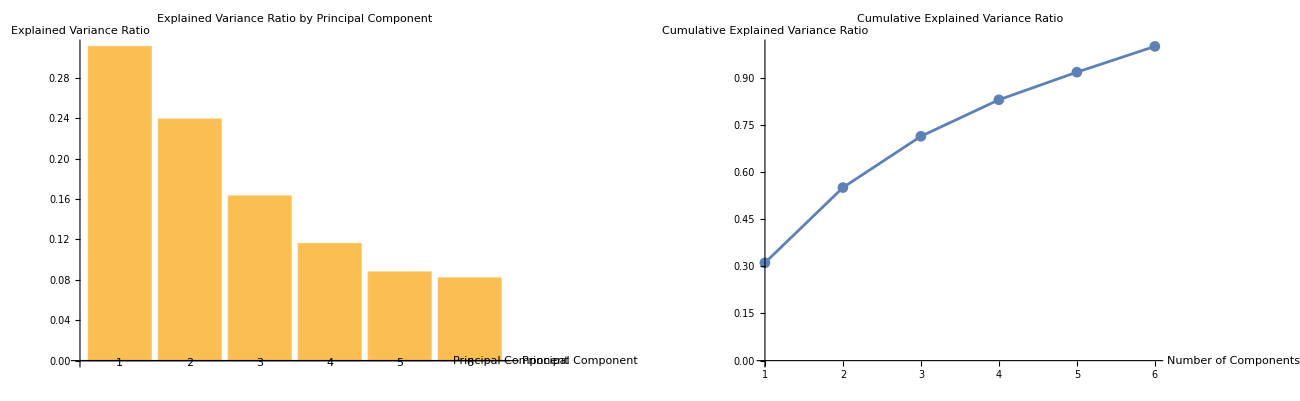

```mathematica
individualVariancePlot=BarChart[explainedVarianceRatio,ChartLabels->Placed[Range[Length[explainedVarianceRatio]],Axis],AxesLabel->{"Principal Component","Explained Variance Ratio"},PlotLabel->"Explained Variance Ratio by Principal Component",ImageSize->300];

cumulativeVariancePlot=ListLinePlot[cumulativeExplainedVarianceRatio,PlotMarkers->Automatic,AxesLabel->{"Number of Components","Cumulative Explained Variance Ratio"},PlotLabel->"Cumulative Explained Variance Ratio",PlotRange->{{1,6},{0,1}},Ticks->{Range[6],Automatic},ImageSize->300];

GraphicsGrid[{{individualVariancePlot,cumulativeVariancePlot}}, Spacings->{1,1},ImageSize->1300,Dividers->{{False,{True},False}},FrameStyle->LightGray,Spacings->{2,{Automatic,{1->-90}}}]
```

```mathematica
percentageExplained=100*explainedVarianceRatio;
TableForm[Transpose[{Range[Length[percentageExplained]],percentageExplained}],TableHeadings->{None,{"Principal Component","% Variance Explained"}}]
```

Principal Component | % Variance Explained
1 | 31.1285
2 | 23.9409
3 | 16.3242
4 | 11.6125
5 | 8.79076
6 | 8.20308

```mathematica
(*Compute the principal components*)reducerPCA=DimensionReduction[allPersMeanOfDiff[[All,18]],6,Method->"PrincipalComponentsAnalysis"];
basisMatrix=reducerPCA["BasisMatrix"];

(*Project the original data onto the principal components*)
reducedData=allPersMeanOfDiff[[All,18]].basisMatrix;

(*Optionally:Verify the explained variances*)
variancesExplained=Variance/@Transpose[reducedData];
totalVariance=Total[variancesExplained];
explainedVarianceRatio=variancesExplained/totalVariance;
cumulativeExplainedVarianceRatio=Accumulate[explainedVarianceRatio];

(*Visualization plots as before*)
individualVariancePlot=BarChart[explainedVarianceRatio,ChartLabels->Placed[Range[Length[explainedVarianceRatio]],Axis],AxesLabel->{"Principal Component","Explained Variance Ratio"},PlotLabel->"Explained Variance Ratio by Principal Component",ImageSize->300];

cumulativeVariancePlot=ListLinePlot[cumulativeExplainedVarianceRatio,PlotMarkers->Automatic,AxesLabel->{"Number of Components","Cumulative Explained Variance Ratio"},PlotLabel->"Cumulative Explained Variance Ratio",PlotRange->{{1,6},{0,1}},Ticks->{Range[6],Automatic},ImageSize->300];

GraphicsGrid[{{individualVariancePlot,cumulativeVariancePlot}},Spacings->{1,1},ImageSize->1300,Dividers->{{False,{True},False}},FrameStyle->LightGray,Spacings->{2,{Automatic,{1->-90}}}]
```

DimensionReducerFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value (BasisMatrix).

BarChart::ldata: Divide[Transpose[Variance[{{0.0128174, -0.00964355, 0.0030365, 0.013916, <<9>>8, <<4089>>, -0.00154877, 0.00201416}, <<155>>} . <<1>>]], Total[<<1>>]] is not a valid dataset or list of datasets.

DimensionReducerFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value (BasisMatrix).

General::stop: Further output of DimensionReducerFunction::mlincfttp will be suppressed during this calculation.

ListLinePlot::lpn: Divide[Annotation[Annotation[Power[Total[Transpose[Variance[{{<<9>>, <<4095>>}, <<155>>} . <<1>>]]], -1] + <<7>>se[<<1>>], C<<19>>#2], <<21>>1], <<1>>] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

BarChart::ldata: Divide[Transpose[Variance[{{0.0128174, -0.00964355, 0.0030365, 0.013916, <<9>>8, <<4089>>, -0.00154877, 0.00201416}, <<155>>} . <<1>>]], Total[<<1>>]] is not a valid dataset or list of datasets.

DimensionReducerFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value (BasisMatrix).

General::stop: Further output of DimensionReducerFunction::mlincfttp will be suppressed during this calculation.

ListLinePlot::lpn: Divide[Annotation[Annotation[Power[Total[Transpose[Variance[{{<<9>>, <<4095>>}, <<155>>} . <<1>>]]], -1] + <<7>>se[<<1>>], C<<19>>#2], <<21>>1], <<1>>] is not a list of numbers or pairs of numbers.

BarChart::ldata: Divide[Transpose[Variance[{{0.0128174, -0.00964355, 0.0030365, 0.013916, <<9>>8, <<4089>>, -0.00154877, 0.00201416}, <<155>>} . <<1>>]], Total[<<1>>]] is not a valid dataset or list of datasets.

ListLinePlot::lpn: Divide[Annotation[Annotation[Power[Total[Transpose[Variance[{{<<9>>, <<4095>>}, <<155>>} . <<1>>]]], -1] + <<7>>se[<<1>>], C<<19>>#2], <<21>>1], <<1>>] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

BarChart::ldata: Divide[Transpose[Variance[{{0.0128174, -0.00964355, 0.0030365, 0.013916, <<9>>8, <<4089>>, -0.00154877, 0.00201416}, <<155>>} . <<1>>]], Total[<<1>>]] is not a valid dataset or list of datasets.

General::stop: Further output of BarChart::ldata will be suppressed during this calculation.

```mathematica
analyzeReducedData[data_,numComponents_]:=Module[{pca,reducedData,reconstructedData,mse,originalDim,pcaDim},originalDim=Dimensions[data];
Print["Original data dimensions: ",originalDim];
pca=PrincipalComponents[data];
pcaDim=Dimensions[pca];
Print["PCA dimensions: ",pcaDim];
If[numComponents>Min[pcaDim],Print["Warning: Requested components (",numComponents,") exceed available components (",Min[pcaDim],"). Using all available components."];
numComponents=Min[pcaDim];];
reducedData=data.Transpose[pca[[1;;numComponents]]];
Print["Reduced data dimensions: ",Dimensions[reducedData]];
reconstructedData=reducedData.pca[[1;;numComponents]];
Print["Reconstructed data dimensions: ",Dimensions[reconstructedData]];
mse=Mean[(data-reconstructedData)^2];
{"NumComponents"->numComponents,"ReducedData"->reducedData,"ReconstructedData"->reconstructedData,"MSE"->mse,"ExplainedVarianceRatio"->Total[Variance/@Transpose[reducedData]]/Total[Variance/@Transpose[data]]}]
```

```mathematica
results=Table[Print["\n--- Analysis for ",i," components ---"];
analyzeReducedData[allPersMeanOfDiff[[All,18]],i],{i,3,5}]
```

--- Analysis for 3 components ---

Original data dimensions: {156,4096}

PCA dimensions: {156,4096}

Reduced data dimensions: {156,3}

Reconstructed data dimensions: {156,4096}

--- Analysis for 4 components ---

Original data dimensions: {156,4096}

PCA dimensions: {156,4096}

Reduced data dimensions: {156,4}

Reconstructed data dimensions: {156,4096}

--- Analysis for 5 components ---

Original data dimensions: {156,4096}

PCA dimensions: {156,4096}

Reduced data dimensions: {156,5}

Reconstructed data dimensions: {156,4096}